```mathematica
h[x_,a_,b_, c_]:=Cos[Sqrt[2b] x]-(2c)/(b + c)*Sin[Sqrt[b/2]]/Sqrt[2b]
```

```mathematica
d[a_, b_, c_] :=h[0, a, b, c]+a Integrate[h[y, a, b, c],{y, -1/2,1/2}]+b Integrate[Abs[y] h[y,a, b, c], {y, -1/2, 1/2}] + c Integrate[y^2 h[y,a, b, c], {y, -1/2, 1/2}]
```

```mathematica
g[x_, a_, b_, c_]:=h[x, a, b, c]/d[a, b, c]
```

Expand g[x, a, b, c] and then use simplify to obtain a nice closed form expression for g (which in Mathematica we call G). This is the solution for m(x) = -a - b |x| - c |x|^2

```mathematica
G[x_, a_, b_, c_]:= (6 b^(3/2) (b+c) Cos[√2 √b x]-6 √2 b c Sin[(√b)/(√2)])/(6 √b (b+c)^2 Cos[(√b)/(√2)]+√2 (6 a b^2+3 b^3+3 b^2 c+b (-12+c) c-6 c^2) Sin[(√b)/(√2)])
```

The kernel of the unitary group is (phi hat (x))/(phi hat (0))(1 - |x|) supported on [-1, 1]. Assuming phi hat (0) = 1 and the kernel is a quadratic, phi hat (x) = a |x| + 1. The kernel therefore is of the form - a |x|^2 + (a - 1) |x| + 1, so following our derivation of g, we have -2 < a < 1 (this ensures the period of g is non-imaginary). The main issue is of course phi is only non-negative when a = -1, i.e. the original kernel.

```mathematica
F[a_]:=1/(a+2)*1/Integrate[G[x, -1, 1 - a, a],{x, -1/2, 1/2}]
```

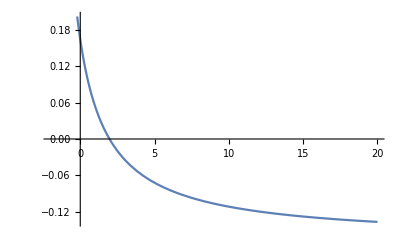

```mathematica
Plot[F[a], {a, -2,20}]
```

Closed form expression of phi for phi hat = (a |x| + 1) supported on [-1, 1]

```mathematica
P[x_, a_]:=2Integrate[Cos[-2 π  x y](1 + a y) ,{y, 0, 1}]
```

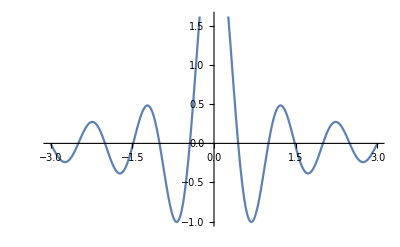

```mathematica
Plot[P[x, 1], {x, -3, 3}]
```

```mathematica
(-a+a Cos[2 π x]+2 (1+a) π x Sin[2 π x])/(2 π^2 x^2)
```

```mathematica
1/Integrate[G[x, -1, 2, -1], {x, -1/2, 1/2}]
```

1/12 (4+3 Cot[1])

```mathematica
N[1/12 (4+3 Cot[1])]
```

0.493856

```mathematica
1/Integrate[G[ x, -5, 10, -5],{x, -1/2, 1/2}]
```

1/12 (-16+3 √5 Cot[√5])

```mathematica
N[1/12 (-16+3 √5 Cot[√5])]
```

-1.77193

```mathematica
(3/2)/Integrate[G[x, -3/2, 8/3, -4/3],{x, -1/2, 1/2}]
```

1/24 (1+6 √3 Cot[2/(√3)])

```mathematica
N[1/24 (1+6 √3 Cot[2/(√3)])]
```

0.233014

Orthogonal verification of consistency

```mathematica
h[y_]:=Piecewise[{{-(54 (-6+3 y+6 Cos[4/(√3)]-3 y Cos[4/(√3)]+3 Cos[(4 (-1+y))/(√3)]-7 Cos[(4 y)/(√3)]+4 y Cos[(4 y)/(√3)]+√3 Sin[(4 (-1+y))/(√3)]))/(6 √3 Cos[2/(√3)]+13 Sin[2/(√3)])^2, 0<y<1}, {(54 (6+3 y-6 Cos[4/(√3)]-3 y Cos[4/(√3)]+7 Cos[(4 y)/(√3)]+4 y Cos[(4 y)/(√3)]-3 Cos[(4 (1+y))/(√3)]+√3 Sin[(4 (1+y))/(√3)]))/(6 √3 Cos[2/(√3)]+13 Sin[2/(√3)])^2, -1<y≤0}, {0, True}}]
```

```mathematica
1/Integrate[h[x], {x, -1, 1}](3/2(h[0] + 1/2 Integrate[h[x], {x, -1, 1}])-2Integrate[(1 - Abs[x])(1 - Abs[x])h[x], {x, -1, 1}] - 1/2 Integrate[h[x], {x, -1, 1}])
```

1/1296 Csc[2/(√3)]^2 (6 √3 Cos[2/(√3)]+13 Sin[2/(√3)])^2 (-(648 Sin[2/(√3)]^2)/(6 √3 Cos[2/(√3)]+13 Sin[2/(√3)])^2+(27 (-32+20 Cos[4/(√3)]+3 √3 Sin[4/(√3)]))/(6 √3 Cos[2/(√3)]+13 Sin[2/(√3)])^2+3/2 ((648 Sin[2/(√3)]^2)/(6 √3 Cos[2/(√3)]+13 Sin[2/(√3)])^2+(54 (13-9 Cos[4/(√3)]+√3 Sin[4/(√3)]))/(6 √3 Cos[2/(√3)]+13 Sin[2/(√3)])^2))

```mathematica
N[%18]
```

0.733014

```mathematica
(3/2)/(Integrate[G[x, -7/6, 8/3, -4/3],{x, -1/2, 1/2}])
```

1/24 (13+6 √3 Cot[2/(√3)])

```mathematica
N[1/24 (13+6 √3 Cot[2/(√3)])]
```

0.733014

Symplectic verification of consistency

```mathematica
(1/2)/(Integrate[G[x,-5/2,8,-6],{x, -1/2,1/2}])
```

1/32 (3+2 Cot[2])

```mathematica
N[1/32 (3+2 Cot[2])]
```

0.0651464

```mathematica
G[x,-5/2,8,-6]
```

(192 √2 Cos[4 x]+288 √2 Sin[2])/(48 √2 Cos[2]+72 √2 Sin[2])

```mathematica
Convolve[Piecewise[{{(192 √2 Cos[4 x]+288 √2 Sin[2])/(48 √2 Cos[2]+72 √2 Sin[2]),x>-1/2&&x<1/2}}],Piecewise[{{(192 √2 Cos[4 x]+288 √2 Sin[2])/(48 √2 Cos[2]+72 √2 Sin[2]),x>-1/2&&x<1/2}}],x,y]
```

Piecewise[{{(8 (12-9 y-12 Cos[4]+9 y Cos[4]-3 Cos[4-4 y]+7 Cos[4 y]-4 y Cos[4 y]+Sin[4-4 y]))/(2 Cos[2]+3 Sin[2])^2, 0<y<1}, {(8 (4 Cos[4 y]+4 y Cos[4 y]+24 Sin[2]^2+18 y Sin[2]^2+6 Sin[2] Sin[2+4 y]+Sin[4+4 y]))/(2 Cos[2]+3 Sin[2])^2, -1<y≤0}, {0, True}}]

Phi Hat for Symplectic

```mathematica
p[y_]:=Piecewise[{{(8 (12-9 y-12 Cos[4]+9 y Cos[4]-3 Cos[4-4 y]+7 Cos[4 y]-4 y Cos[4 y]+Sin[4-4 y]))/(2 Cos[2]+3 Sin[2])^2, 0<y<1}, {(8 (4 Cos[4 y]+4 y Cos[4 y]+24 Sin[2]^2+18 y Sin[2]^2+6 Sin[2] Sin[2+4 y]+Sin[4+4 y]))/(2 Cos[2]+3 Sin[2])^2, -1<y≤0}, {0, True}}]
```

```mathematica
c[x_]:=Piecewise[{{1, -1 < x < 1}}]
```

```mathematica
1/Integrate[p[x],{x, -1, 1}]((1/2) (p[0]-Integrate[p[x],{x, -1, 1}]/2) -2Integrate[(1 - Abs[x])(1 - Abs[x])p[x],{x, -1, 1}]  +Integrate[p[x](1 - Abs[y])c[Abs[x] + Abs[y]],{x, -1, 1},{y, -1, 1}] )
```

1/256 Csc[2]^2 (2 Cos[2]+3 Sin[2])^2 (-(8 (-13+13 Cos[4]+2 Sin[4]))/(2 Cos[2]+3 Sin[2])^2+(4 (-34+30 Cos[4]+5 Sin[4]))/(2 Cos[2]+3 Sin[2])^2+1/2 (-(128 Sin[2]^2)/(2 Cos[2]+3 Sin[2])^2+(8 (4+30 Sin[2]^2+Sin[4]))/(2 Cos[2]+3 Sin[2])^2))

```mathematica
N[%25]
```

0.0651464